## Convert Covid-19 Cases

```mathematica
path0=NotebookDirectory[];
coviddata=Import[path0<>"covid.csv","CSV"];
days=DayCount[coviddata[[2,4]],coviddata[[-1,4]]]
cases=coviddata[[2;;,6]];
death=coviddata[[2;;,9]];
```

697

```mathematica
avgcase=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@cases[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
avgdeath=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@death[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
Export[path0<>"cases.csv",{avgcase},"CSV"];
Export[path0<>"casesD.csv",{avgdeath*1/0.0037},"CSV"];
```

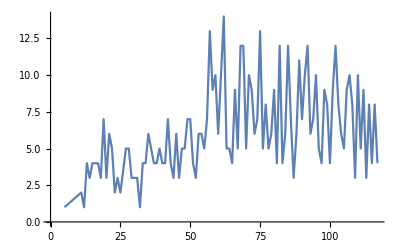

```mathematica
path0=NotebookDirectory[];
cases=Import[path0<>"casesD.csv","CSV"][[1]];
Table[{i,RandomVariate[BinomialDistribution[Floor@cases[[i]],5*10^-7],1][[1]]},{i,1,Length[cases]}];
data=Select[%,#[[2]]>0&];
ListPlot[data,Joined->True]
```

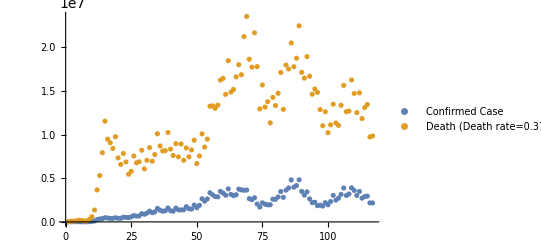

```mathematica
ListPlot[{avgcase,1/0.0037*avgdeath},PlotLegends->{"Confirmed Case","Death (Death rate=0.37%)"}]
```

```mathematica
(*Functions*)
TDeltaT[lineage_,n_]:=
Module[{t0},
t0=lineage[[1]];
{t0,lineage[[n+1]]}
]
getDeltaT[lineagelist_,n_]:=TDeltaT[#,n]&/@lineagelist

path0=NotebookDirectory[];
k = {1,2,3};
lineage=Import[path0<>"data/N2.0E+07K"<>ToString[#]<>"M1E-05A.out","CSV"]&/@k;
(*lineageA=Import[path0<>"data/K"<>ToString[#]<>"M5E-05A.out","CSV"]&/@k;*)
Mean/@lineage[[1;;3,;;,1]]//N(*T*)
Mean/@lineage[[1;;3,;;,2]]//N(*DeltaT*)
Dimensions/@lineage
```

{1.,23.334,109.923}

{4.163,4.716,7.148}

{{1000},{1000},{1000}}

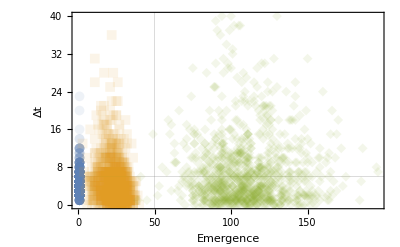

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},PlotStyle->Opacity[0.1],GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]
```

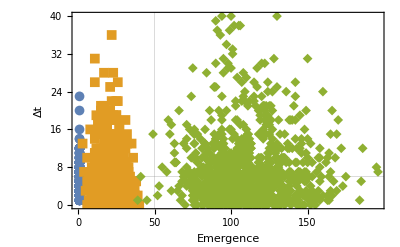

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]

Histogram3D[Append[DataTDeltaT,actual],Automatic,"Probability",ChartLabels->Placed[{"k=1","k=2","k=3","Real"},Above,"Framed"]]
```

## Dirichlet Multinomial Sampling

```mathematica
(*One genotype with n individuals*)
cond = {r->2,p->0.2,n->3,runs->10000};
distInd=NegativeBinomialDistribution[r,p]/.cond;
rand=RandomVariate[distInd,{runs,n}/.cond];
sumOfInd=Plus@@@rand;
distSum=NegativeBinomialDistribution[r*n,p]/.cond;
randSum=RandomVariate[distSum,runs/.cond];
```

```mathematica
Mean@sumOfInd//N
Mean@randSum//N
Variance@sumOfInd//N
Variance@randSum//N
```

24.1396

24.0297

123.33

119.547

```mathematica
(*2 genotypes with n_i individuals*)
cond = {rn1->2,p1->0.2,rn2->3,p2->0.1,runs->1000};
dist1=NegativeBinomialDistribution[rn1,p1]/.cond;
dist2=NegativeBinomialDistribution[rn2,p2]/.cond;
n1=RandomVariate[dist1,runs/.cond];
n2=RandomVariate[dist2,runs/.cond];
nTot=n1+n2;
```

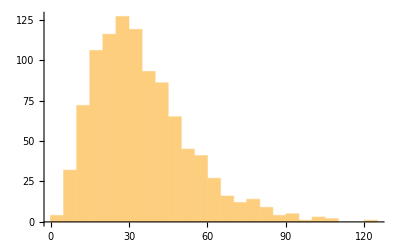

```mathematica
Histogram[nTot]
```